```mathematica
Clear["Global`*"]
```

## Counts the number of travelling waves

General constraints for travelling waves (even grid size)

```mathematica
conds= {
n1p+n2p/2+n3m/2-n1m-n2m/2-n3p/2 == Wx*gz &&
n2p+n3p-n2m-n3m==Wy*gz  &&
n1p+n1m+n2p+n2m+n3p+n3m ==nc*gz &&
0 ≤ n1p ≤ nc*gz &&
0 ≤ n1m ≤ nc*gz &&
0 ≤ n2p ≤ nc*gz &&
0 ≤ n2m ≤ nc*gz &&
0 ≤ n3p ≤ nc*gz &&
0 ≤ n3m ≤ nc*gz &&
gz ∈ Integers
};
```

```mathematica
Solve[conds  /. {Wx->1, Wy ->-1, nc-> 3/2}, {n1p, n1m, n2p, n2m, n3p, n3m}, Integers]
```

{{n1p→ConditionalExpression[C[1],C[1]∈ℤ&&C[1]≥0&&gz==2 C[1]],n1m→ConditionalExpression[0,C[1]∈ℤ&&C[1]≥0&&gz==2 C[1]],n2p→ConditionalExpression[0,C[1]∈ℤ&&C[1]≥0&&gz==2 C[1]],n2m→ConditionalExpression[0,C[1]∈ℤ&&C[1]≥0&&gz==2 C[1]],n3p→ConditionalExpression[0,C[1]∈ℤ&&C[1]≥0&&gz==2 C[1]],n3m→ConditionalExpression[2 C[1],C[1]∈ℤ&&C[1]≥0&&gz==2 C[1]]}}

Estimate the total number of waveforms
Estimate phase space density

```mathematica
thisgz = 16;
thisnWavesMax = Floor[(thisgz-1)/4]; (*Max number of waves*)
WTable= {{1,0},{0,1}, {1,1}, {1,2},{2,1},{1,3}}; (*all values of (Wx, Wy)*)
(*DTable = {1, 1, 2, 2, 2 ,2}; *)(*multiplicity due to Wx->-Wx, Wy-> -Wy symmetry*)
DTable = Map[Boole[#>1 ]&,Total/@WTable]+1;
NwfTable={1,Binomial[gz,gz/2], Binomial[3/2gz, gz/2], 1, Binomial[5/2gz, gz],Binomial[3gz, gz/2]};
NcTable = {1, 1, 3/2, 2, 5/2,3};
TTable = {gz, gz,2gz,2gz,2gz,gz^2};(*periods*)
nwaveDist = {1, (gz-6)/2, gz}; (*number of possible distances between waves*)
NwaveStates = Sum[Total[ndir *nwaveDist[[nwaves]]*DTable*(NwfTable)^nwaves] , {nwaves, 1, 2}]/. {gz -> thisgz,
ndir-> 2, nWavesMax -> thisnWavesMax}; (*total number of waves states*)
NwaveDensity = NwaveStates/(2^(gz^2)) /. {gz -> thisgz};
Print["Number of wave states = ", N[NwaveStates]]
Print["Phase space density = ", N[NwaveDensity]]
```

Number of wave states = 7.90106×10^22

Phase space density = 6.82349×10^-55

```mathematica
gzlist=Range[8, 50, 2];
NwaveStatesList = Table[
Sum[ Total[ndir *nwaveDist[[nwaves]]*DTable*(NwfTable)^nwaves]/. 
{gz -> gzlist[[i]],ndir-> 2, nWavesMax -> thisnWavesMax} , {nwaves, 1, 2}],
{i, 1,Length[gzlist]}];
NwaveDensityList = NwaveStatesList/(2^(gzlist^2));
```

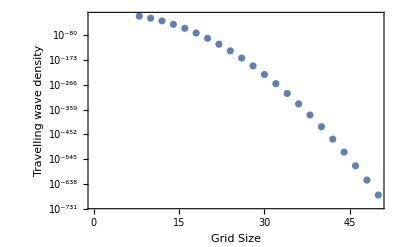

```mathematica
ListLogPlot[Transpose[{gzlist, NwaveDensityList}], Frame-> True, FrameLabel->{"Grid Size", "Travelling wave density"}]
```